```mathematica
(* red-green calculus standard defns *)
```

```mathematica
<<Combinatorica`;
id=IdentityMatrix[2];
T[]:={{1}};
T[X_]:=X;
T[X_,Y__]:=Simplify[Fold[KroneckerProduct,X,{Y}]];
id2[n_]:=T@@Table[id,{n}];
Dag[X_]:=ConjugateTranspose[X];
rootd=Sqrt[2];
h={{1,1},{1,-1}};
b0={{1},{0}};b1={{0},{1}};
compbasis={b0,b1};
PermutedTensor[perm_]:=(perm1=Function[x,x+1]/@perm;
Function[p,Permute[p,perm1]]/@Tuples[{1,2},Length[perm1]]);
sig[perm__]:=Function[t,Flatten[T@@t]]/@Function[b,compbasis[[b]]]/@PermutedTensor[{perm}];
zsp[angle_,in_,out_]:=SparseArray[{{1,1}-> 1, {2^out,2^in}-> ⅇ^(ⅈ angle)}];
xsp[angle_,in_,out_]:=(1/2)*
T@@Table[h,{out}].zsp[angle,in,out].T@@Table[h,{in}];
```

```mathematica
(* Output generated by quantomatic *)
```

```mathematica
lhs=Simplify[(id2[1].xsp[0,2,1].sig[1,0].T[zsp[α,1,1],zsp[β,1,1]].xsp[0,1,2].id2[1])];lhs//MatrixForm
```

(1+ⅇ^(ⅈ (α+β)) | 0
0 | ⅇ^(ⅈ α)+ⅇ^(ⅈ β))

```mathematica
rhs=(xsp[γ,0,1].xsp[δ,1,0]);rhs//MatrixForm
```

(1/4 (1+ⅇ^(ⅈ γ)) (1+ⅇ^(ⅈ δ)) | 1/4 (1+ⅇ^(ⅈ γ)) (1-ⅇ^(ⅈ δ))
1/4 (1-ⅇ^(ⅈ γ)) (1+ⅇ^(ⅈ δ)) | 1/4 (1-ⅇ^(ⅈ γ)) (1-ⅇ^(ⅈ δ)))

```mathematica
Simplify[Reduce[k*lhs==rhs,{α,β,γ,δ,k}]]
```

(C[1]|C[2]|C[3])∈Integers&&((k==1/(ⅇ^(ⅈ α)+ⅇ^(ⅈ β))&&π+2 π C[1]==γ&&π+2 π C[2]==δ&&π+2 π C[3]==α+β&&ⅇ^(ⅈ α)+ⅇ^(ⅈ β)≠0)||(k==1/(1+ⅇ^(ⅈ (α+β)))&&γ==2 π C[1]&&δ==2 π C[2]&&β+ⅈ Log[-ⅇ^(ⅈ α)]==2 π C[3]&&ⅇ^(ⅈ α)≠0&&1+ⅇ^(ⅈ (α+β))≠0))

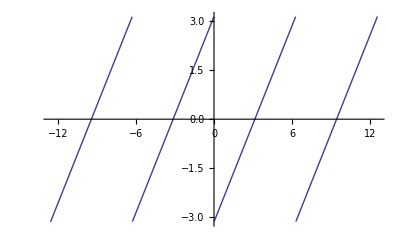

```mathematica
Plot[-ⅈ Log[ⅇ^(ⅈ (a+π))] ,{a,-4 π,4 π}]
```

```mathematica
Reduce[ⅈ p==Log[ⅇ^(ⅈ a)]&&p∈Reals,{a}]
```

C[1]∈Integers&&-π<p≤π&&a==-ⅈ (2 ⅈ π C[1]+Log[ⅇ^(ⅈ p)])

```mathematica
Reduce[Cos[a]==  Cos[π-b]&&{a,b}∈Reals,{a}]
```

b∈Reals&&C[1]∈Integers&&(a==-ArcCos[-Cos[b]]+2 π C[1]||a==ArcCos[-Cos[b]]+2 π C[1])

```mathematica
4+4
```

8